#### Physics Applications

Evolving a single qubit, creating CNOT.

```mathematica
onequbit = QuantumFiniteDimensionalState[{{1,0}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
$hbar = 1;
```

```mathematica
$epsilon = 1;
```

```mathematica
$t = 1;
```

```mathematica
matrixHamiltonian1 = {{$epsilon,$t},{$t,-$epsilon}};
```

```mathematica
operatorU[t_,hamiltonian_] := QuantumMatrixOperation[N[Cos[hamiltonian*t/$hbar],10]- I*N[Sin[hamiltonian*t/$hbar],10]]
```

```mathematica
qubitEvolve[t_,operator_,initialqubit_,hamiltonian_]:=QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1}-> operator[t,hamiltonian],initialqubit]["StateVector"]]}]]
```

```mathematica
qubitEvolution[operator_,initialqubit_,hamiltonian_]:=qubitEvolve[#,operator,initialqubit,hamiltonian]&/@Range[0,4*Pi,0.5]
```

```mathematica
showQubitEvolution[operator_,initialqubit_,hamiltonian_]:= GraphicsGrid[{showState[separateStates[qubitEvolution[operator,initialqubit,hamiltonian]]]},ItemAspectRatio->2]
```

```mathematica
showQubitEvolution[operatorU,onequbit, matrixHamiltonian1]
```

-Graphics-

```mathematica
(* increase epsilon and decrease t*)
```

```mathematica
ClearAll[$epsilon,$t,matrixHamiltonian1]
```

```mathematica
(*$t = 0.5;*)
$epsilon= 2;
```

```mathematica
showQubitEvolution[operatorU,onequbit,matrixHamiltonian1]
```

-Graphics-

```mathematica
showQubitEvolution[operatorU,onequbit,matrixHamiltonian1]
```

-Graphics-

```mathematica
Dynamic[MouseAnnotation[]]
```

```mathematica
{showQubitEvolution[operatorU,#,matrixHamiltonian1]}&/@initialState[5]
```

{{-Graphics-},{-Graphics-},{-Graphics-}}

#### Precession

```mathematica
omega = 1;
B = 1;
```

```mathematica
operatorPrecession[t_] := QuantumMatrixOperation[{{N[Cos[omega*t],10]+ I*N[Sin[omega*t]],0},{N[Cos[omega*t],10]- I*N[Sin[omega*t]],0}}]
```

```mathematica
qubitEvolveP[t_,operator_,initialqubit_]:=QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1}-> operator[t],initialqubit]["StateVector"]]}]]
```

```mathematica
qubitEvolutionP[operator_,initialqubit_]:=qubitEvolveP[#,operator,initialqubit]&/@Range[0,25,0.5]
```

```mathematica
showQubitEvolutionP[operator_,initialqubit_]:= GraphicsGrid[{showState[separateStates[qubitEvolutionP[operator,initialqubit]]]},ItemAspectRatio->2]
```

```mathematica
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

```mathematica
Dynamic[MouseAnnotation[]]
```

```mathematica
omega = 0.5;
```

```mathematica
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

```mathematica
omega = 2;
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

#### Coupled 2 Two State Systems

```mathematica
twoqubits = QuantumFiniteDimensionalState[{{1,0},{1,0}}]
```

QuantumFiniteDimensionalState[…]

```mathematica
operatorU2[t_,hamiltonian_]:=QuantumMatrixOperation[N[Cos[hamiltonian*t/$hbar],10]- I*N[Sin[hamiltonian*t/$hbar],10]]
```

```mathematica
qubitEvolve2[t_,operator_,hamiltonian_,initialqubit_]:= QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1,2}-> operator[t,hamiltonian],initialqubit]["StateVector"]]}]]
```

```mathematica
qubitEvolution2[operator_,initialqubit_]:=qubitEvolve2[#,operator,matrixHamiltonian2,initialqubit]&/@Range[0,5,0.5]
```

```mathematica
colourQubit2[qubit_]:= {getColour[qubit⟦1⟧],getColour[qubit⟦2⟧],getColour[qubit⟦3⟧],getColour[qubit⟦4⟧]}
```

```mathematica
colourState2[state_]:=Map[colourQubit2,state]
```

```mathematica
showQubit2[qubit_]:= Annotation[Rotate[ArrayPlot[{colourQubit2[qubit]},Frame-> False,PlotRangePadding->None, ImageSize->Small],3Pi/2],qubit,"Mouse"]
```

```mathematica
showState2[state_]:=Map[showQubit2,state]
```

```mathematica
GraphicsGrid[{showState2[separateStates[qubitEvolution2[operatorU2,twoqubits]]]}]
```

-Graphics-

#### Heisenberg Spin Chains (NN interactions)

```mathematica
hamiltonianTimeX[t_]:= QuantumMatrixOperation[N[Cos[{{0,1},{1,0}}*t/$hbar]]- I*N[Sin[{{0,1},{1,0}}*t/$hbar]]]
```

```mathematica
hamiltonianTimeY[t_]:= QuantumMatrixOperation[N[Cos[{{0,-I},{I,0}}*t/$hbar]]- I*N[Sin[{{0,-I},{I,0}}*t/$hbar]]]
```

```mathematica
hamiltonianTimeZ[t_]:= QuantumMatrixOperation[N[Cos[{{1,0},{0,-1}}*t/$hbar]]- I*N[Sin[{{1,0},{0,-1}}*t/$hbar]]]
```

```mathematica
nextQubitH[t_,j_Integer,states_]:= Normalize[Normal[QuantumEvaluate[{j}-> hamiltonianTimeX[t],QuantumEvaluate[{j+1}->hamiltonianTimeX[t],states]]["StateVector"]] + Normal[QuantumEvaluate[{j}-> hamiltonianTimeY[t],QuantumEvaluate[{j+1}->hamiltonianTimeY[t],states]]["StateVector"]]+ Normal[QuantumEvaluate[{j}-> hamiltonianTimeZ[t],QuantumEvaluate[{j+1}->hamiltonianTimeZ[t],states]]["StateVector"]]]/;j≠ Log[2,Length[Normal[states["StateVector"]]]]

nextQubitH[t_,j_Integer,states_]:= Normalize[Normal[QuantumEvaluate[{j}-> hamiltonianTimeX[t],QuantumEvaluate[{1}->hamiltonianTimeX[t],states]]["StateVector"]] + Normal[QuantumEvaluate[{j}-> hamiltonianTimeY[t],QuantumEvaluate[{1}->hamiltonianTimeY[t],states]]["StateVector"]]+ Normal[QuantumEvaluate[{j}-> hamiltonianTimeZ[t],QuantumEvaluate[{1}->hamiltonianTimeZ[t],states]]["StateVector"]]]/;j=== Log[2,Length[Normal[states["StateVector"]]]]
```

```mathematica
nextStateH[t_,states_]:= Normalize[Total[nextQubitH[t,#,states]&/@Range[Log[2,Length[Normal[states["StateVector"]]]]]]]
```

```mathematica
fullEvolutionH[states_,timeduration_,timestep_]:= Normal[QuantumFiniteDimensionalState[fixStupidity[{nextStateH[#,states]}]]["StateVector"]]&/@Range[0,timeduration,timestep]
```

```mathematica
evolution=fullEvolutionH[QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],10,0.02];
```

```mathematica
evolution[[1]]
```

```mathematica
Norm[#]^2&/@{0.6123724356957946+0. ⅈ,0.4082482904638631+0. ⅈ,0.4082482904638631+0. ⅈ,0.20412414523193154+0. ⅈ,0.4082482904638631+0. ⅈ,0.20412414523193154+0. ⅈ,0.20412414523193154+0. ⅈ,0.+0. ⅈ}
```

```mathematica
norms=Map[Norm[#]^2&,evolution,{2}];
```

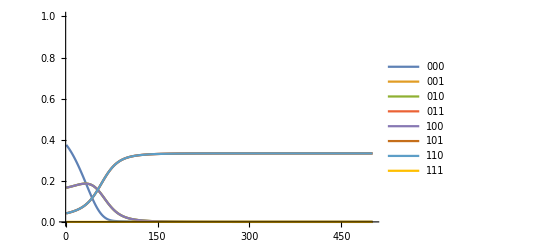

```mathematica
ListLinePlot[Transpose@norms,PlotLegends-> {"000","001","010","011","100","101","110","111"},PlotRange->{0,1}]
```

```mathematica
colourNQubit[qubit_]:= getColour[qubit⟦#⟧]&/@Range[Length[qubit]]
```

```mathematica
showHeisenbergEvolution[states_,timeduration_,timestep_]:= colourNQubit[#]&/@fullEvolutionH[states,timeduration,timestep]
```

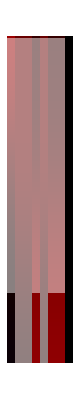

```mathematica
Rotate[ArrayPlot[showHeisenbergEvolution[QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],2,0.01]],Pi/2]
```

trying to examine smaller systems (two qubits with just xx coupling, just yy ...), create your own iSWAP.
examine sudden jump in QCA, and rotate it, norm grayscale visualization to see populations change. population first phase after. 
measures of entanglement, in between states. Neilson and Isaac Chuang intro to QC. 
for noise : projective measurements.